Ramon Ruiz Dolz
Salvador Marti Roman

Computabilidad y complejidad: 3CO21

```mathematica
(*Autómatas Celulares (1)*)
```

```mathematica
ReglaFormato[regla_]:=Module[{rule, listbin, VNnum, i},
rule=regla;
listbin = Reverse[IntegerDigits[rule,2,8]];(*Número decimal expresado en binario de longitud 8*)
VNnum={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};(*Número de Von Neumann*)
For[i=1,i≤ Length[listbin],i++,
(*Añade cada numero del decimal en la posicion i al número de Von Neumann i*)
AppendTo[VNnum[[i]],listbin[[i]]];
];
Return[VNnum];
]
```

```mathematica
ReglaFormato[54]
```

{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}}

```mathematica
Transicion[regla_, estado_] := Module[{ini, fin, i, val, reg, len},
ini=estado;
reg=ReglaFormato[regla];(*Obtenemos la regla expresada adecuadamente*)
fin={};
len=Length[ini];
For[i=0, i< len, i++,
(*Hace matching para saber a que configuración de celula transitar*)
val=Cases[reg,{ini[[len]],ini[[1]],ini[[2]],_}];
val=Flatten[val];
(*Añade a la solución el nuevo valor de la celula*)
AppendTo[fin,val[[4]]];
(*Rota a la izquierda para hacer el matching con la siguiente celula*)
ini=RotateLeft[ini];
];
Return [fin];
]
```

```mathematica
Transicion[54,{1,0,1,0,1,0,1,0,1}]
```

{0,1,1,1,1,1,1,1,0}

```mathematica
ACunidim[estado_, regla_, numtrans_]:=Module[{t, final, reg,i, aux},
t=numtrans;(*Numero de configuraciones a calcular*)
aux=estado;(*Configuracion inicial*)
final={estado};(*Representacion de las transiciones*)
reg=regla;
For[i=0, i<t,i++,
(*Calcula una configuracion por cada numero de configuraciones a calcular y las añade a final*)
aux=Transicion[reg,aux];
AppendTo[final, aux];
];
(*Visualizacion de las iteraciones*)
ArrayPlot[final]
]
```

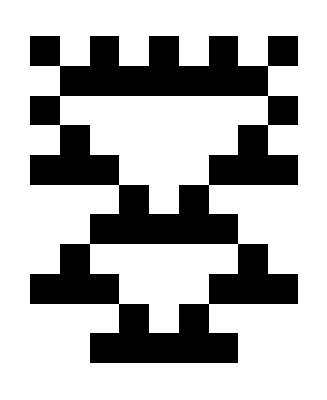

```mathematica
ACunidim[{1,0,1,0,1,0,1,0,1},54,10]
```

```mathematica
ArrayPlot[CellularAutomaton[54,{1,0,1,0,1,0,1,0,1},10]]
```

-Graphics-